```mathematica
(* speed of light *)
c=2.998*10^8;
(* frequency of red light in Hz *)
fRED= c/(750*10^-9);
fVIOLET= c/(380*10^-9);
(* Plank's constant *)
h=6.62607*10^-34;
(* a physical constant *)
k=1.38065*10^-23;
(* setting the key to be 2 and red *)
f0=fRED;
base=17;
```

```mathematica
SetDirectory["/Users/jackson/Documents/GitHub/synesthesiaer"];
```

```mathematica
{λ,x,y,z}=Import["http://www.cvrl.org/database/data/cmfs/ciexyzjv.csv"]ᵀ;
(*convert λ to m*)
λ=10^-9*λ;
```

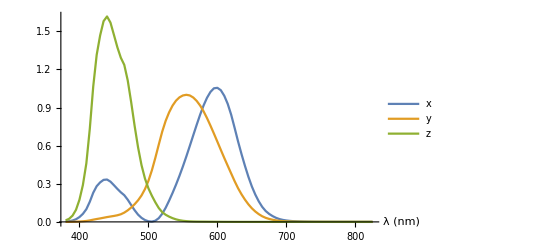

```mathematica
ListLinePlot[{{10^9*λ,x}ᵀ,{10^9*λ,y}ᵀ,{10^9*λ,z}ᵀ},PlotLegends->{"x","y","z"},AxesLabel->{"λ (nm)"}]
```

```mathematica
xtable=Table[{λ[[i]],x[[i]]},{i,1,Length[λ]}];
ytable=Table[{λ[[i]],y[[i]]},{i,1,Length[λ]}];
ztable=Table[{λ[[i]],z[[i]]},{i,1,Length[λ]}];
```

```mathematica
xbar=Interpolation[xtable];
ybar=Interpolation[ytable];
zbar=Interpolation[ztable];
```

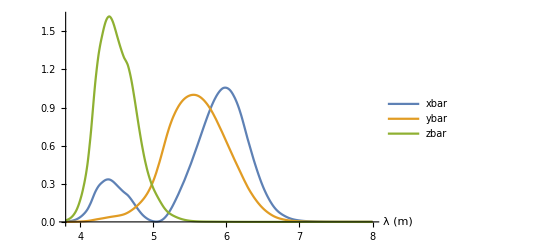

```mathematica
Plot[{xbar[λ],ybar[λ],zbar[λ]},{λ,380*10^-9,800*10^-9},PlotLegends->{"xbar","ybar","zbar"},AxesLabel->{"λ (m)"}]
```

```mathematica
(* frequency associated to a prime number *)
f[b_,p_]:=f0*Log[b,p]
```

```mathematica
(* perform convolution of power spectrum with color matching functions to obtain XYZ color values *)
XYZ[n_]:=Module[{fac=FactorInteger[n],X,Y,Z},
X=Sum[fac[[i,2]]*xbar[ c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Y=Sum[fac[[i,2]]*ybar[c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Z=Sum[fac[[i,2]]*zbar[c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Return[{X,Y,Z}]
]
```

```mathematica
(* assigns a color to a number in a natural way *)
Color[n_]:=ColorConvert[XYZColor@@XYZ[n],"RGB"]
```

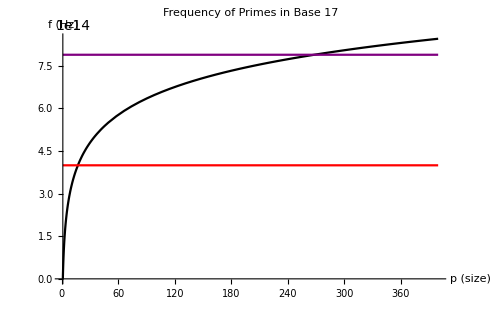

```mathematica
(* generate plot of freq. of each prime for a given base. include visibile range. *)
Plot[{f[p],fRED,fVIOLET},{p,1,400},PlotStyle->{Black,Red,Purple},AxesLabel->{"p (size)","f (Hz)"},PlotLabel->"Frequency of Primes in Base " <> ToString[base]]
```

```mathematica
(* Find the range of available primes/keys*)
pLow=Exp[Log[base]*fRED/f0];
pHigh=Exp[Log[base]*fVIOLET/f0];
```

```mathematica
(* only certain scales are available. *)
```

```mathematica
Color[base]
```

RGBColor[0.010479256224648946, 0., 0.]

```mathematica
NextPrime[16.1]
```

17